Name: Karan Sharma
College Roll No.: 2232191
University Roll No. : 22036563079
Class: BSc (Hons) Mathematics / Year 3 / Complex Analysis
Section: A

# PRACTICAL 4

Show that the image of the open disk D1 = {z: |z + 1 + | < 1} under the linear transformation w = (3–4i) z + 6 + 2i is the open disk centered at  (–1+3i) 
with radius 5, {w: |w + 1 – 3i| < 5}.

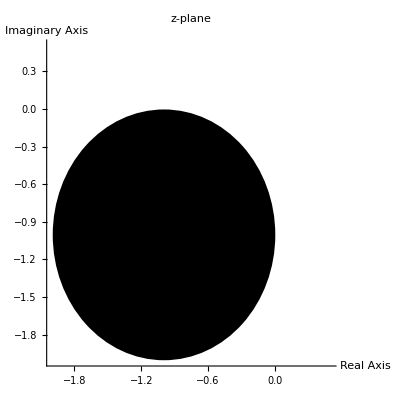

```mathematica
a=Region[Disk[{-1,-1},1],Axes->True,AxesLabel->{"Real Axis", "Imaginary Axis"},PlotLabel->"z-plane",PlotRange->{{-2,0.5},{-2,0.5}}]
```

```mathematica
z=x+ⅈy
```

x+ⅈy

```mathematica
w=ComplexExpand[(3-4ⅈ)z+(6+2ⅈ)]
```

6+3 x+ⅈ (2-4 x-4 ⅈy)+3 ⅈy

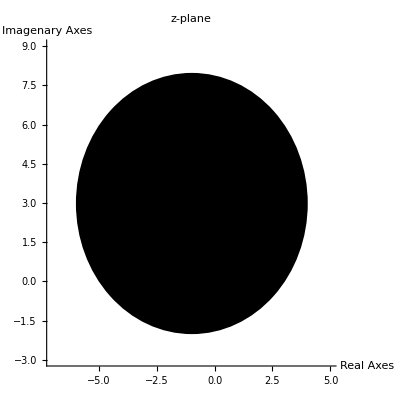

```mathematica
b=Region[
TransformedRegion[a,Function[p,{6+3p[[1]]+4p[[2]],2-4p[[1]]+3p[[2]]}]],
PlotLabel->"w-plane",PlotRange->{{-7,5},{-3,9}}
]
```

```mathematica
RegionCentroid[b]
```

{-1,3}

```mathematica
radius=√(Area[b]/π)
```

5

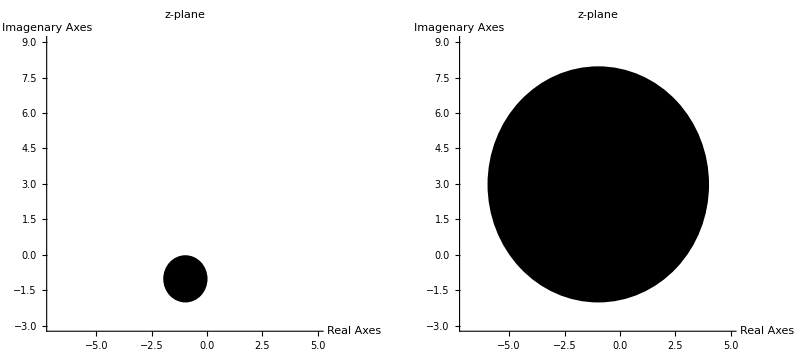

```mathematica
GraphicsRow[{a,b}]
```